In this notebook the external magnetic field of a radially magnetized multipole cylinder is implemented in 2D. The solution is taken from https://iopscience.iop.org/article/10.1088/0022-3727/33/1/305.

## Field outside the cylinder (r>Ro)

```mathematica
M[k_,p_]:=Sum[1/k/π*(-1)^m*(Sin[(2*m-1)/p*k*π]-Sin[(2*m+1)/p*k*π]),{m,1,p}];
```

```mathematica
U2[M_,Ri_,Ro_,k_]:=-H2[M,Ri,Ro,k]/4;
```

```mathematica
H2[M_,Ri_,Ro_,k_]:= Ro^(k+1)*(2/Ro*M/k/(k+1)*(Ro-(Ri/Ro)^k*Ri)-2*M/k+2*M/k*(Ri/Ro)^(k+1));
```

```mathematica
BrCylinderSegment2DOuter[r_,φ_,p_,Ri_,Ro_,nbTerms_]:=(
Sum[k*r^(-(k+1))*U2[M[k,p],Ri,Ro,k]*Cos[k*φ],{k,1,nbTerms}]
);
```

```mathematica
BφCylinderSegment2DOuter[r_,φ_,p_,Ri_,Ro_,nbTerms_]:=(
Sum[k*r^(-(k+1))*U2[M[k,p],Ri,Ro,k]*Sin[k*φ],{k,1,nbTerms}]
);
```

```mathematica
𝕖r[r_,φ_]:={Cos[φ],Sin[φ]};
𝕖φ[r_,φ_]:={-Sin[φ],Cos[φ]};
```

```mathematica
𝔹[y_,z_,p_,Ri_,Ro_,nbTerms_]:=(
rVal=Sqrt[y^2+z^2];
φVal=ArcTan[y,z];
BrCylinderSegment2DOuter[rVal,φVal,p,Ri,Ro,nbTerms]*𝕖r[rVal,φVal]+BφCylinderSegment2DOuter[rVal,φVal,p,Ri,Ro,nbTerms]*𝕖φ[rVal,φVal]
);
```

### Plot

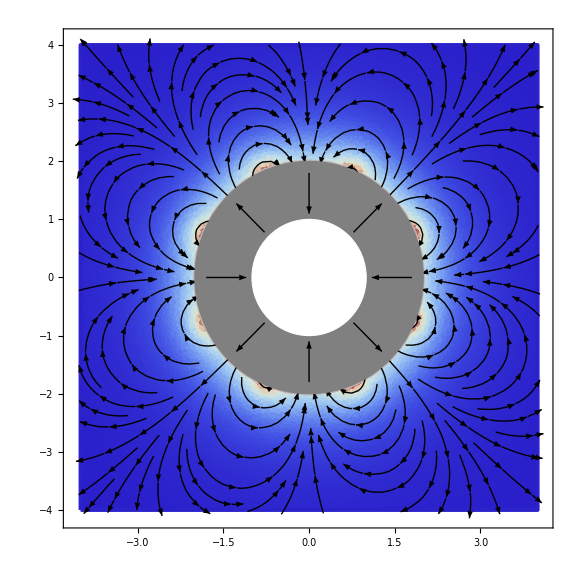

```mathematica
(* plot *)
Ri=1;
Ro=2;
p=8;
magnets=Table[
Graphics[{EdgeForm[Thick],Gray,Disk[{0,0},Ro,{-π/p+2π/p*k,π/p+2π/p*k}]}],{k,1,p}
];
arrows=Table[
Graphics[Arrow[{(0.9*Ro*Mod[k+1,2]+1.1*Ri*Mod[k,2])*{Cos[2π/p*k],Sin[2π/p*k]},(0.9*Ro*Mod[k,2]+1.1*Ri*Mod[k+1,2])*{Cos[2π/p*k],Sin[2π/p*k]}}]],{k,1,p}
];
outerDisk=Disk[{0,0},Ro];
innerDisk=Disk[{0,0},Ri];
rect=Rectangle[{-4, -4},{4,4}];
𝔹plot[y_,z_]=𝔹[y,z,p,Ri,Ro,40];
outerPlot=StreamDensityPlot[Evaluate@𝔹plot[y0,z0],{y0,z0}∈RegionDifference[rect,outerDisk],ColorFunction->ColorData["ThermometerColors"], StreamStyle->Black,StreamColorFunction->None,AspectRatio->Automatic,BoundaryStyle->{Black,Thickness[0.005]}];
cylinderSegmentGear2D=Show[outerPlot,Show@@magnets,Show@@arrows,Graphics[{EdgeForm[Thick],White,innerDisk}],PlotRange->All,ImageSize->Large]
```

```mathematica
Export["cylinderSegmentGear2D.pdf",cylinderSegmentGear2D]
```

cylinderSegmentGear2D.pdf

## Force and torque

```mathematica
𝕖y={1,0,0};
𝕖z={0,1,0};
```

```mathematica
𝕖rp[θp_]:=Cos[θp]*𝕖y+Sin[θp]*𝕖z;
𝕖θp[θp_]:=-Sin[θp]*𝕖y+Cos[θp]*𝕖z;
```

```mathematica
𝕖r[θ_]:=Cos[θ]*𝕖y+Sin[θ]*𝕖z;
𝕖θ[θ_]:=-Sin[θ]*𝕖y+Cos[θ]*𝕖z;
```

```mathematica
rp[r_,θ_]:=Sqrt[r^2+2*r*d*Cos[θ]+d^2];
θp[r_,θ_]:=ArcTan[r*Cos[θ]+d,r*Sin[θ]];
```

```mathematica
𝕟[r_,θ_]:=𝕖θ[θ];
𝕄[r_,θ_]:=M0*𝕖r[θ];
```

```mathematica
Brp[r_,θ_]:=By*Cos[θp[r,θ]]+Bz*Sin[θp[r,θ]];
Bθp[r_,θ_]:=Bz*Cos[θp[r,θ]]-By*Sin[θp[r,θ]];
```

```mathematica
𝔹[r_,θ_]:=Brp[r,θ]*𝕖rp[θp[r,θ]]+Bθp[r,θ]*𝕖θp[θp[r,θ]];
𝕣[r_,θ_]:=r*𝕖r[θ];
```

```mathematica
(𝕄[r,θ]×𝕟[r,θ])×𝔹[r,θ]//Simplify
```

{-Bz M0,By M0,0}

```mathematica
𝕣[r,θ]×((𝕄[r,θ]×𝕟[r,θ])×𝔹[r,θ])//Simplify
```

{0,0,M0 r (By Cos[θ]+Bz Sin[θ])}